# Muscle Static Analysis

## Data Import

```mathematica
imported = Import["/Users/thomasbuhrmann/Experiments/12_05_29__17_17_11/Isometric.txt", "Table"];
varnames = imported[[1]];
data= imported[[2;;Length[imported]-1]];
n = Length[data];
m = Length[varnames];
data = Transpose[data]; (* Each list contains all obervations of a single variable *)
```

## Function Definitions

```mathematica
NtoI[name_] := Position[varnames,name][[1]]; (* Gets the list index for the specified variable name *)
NtoD[name_] :=data[[NtoI[name]]][[1]];(* Gets the data for the specified variable name *)
time = NtoD["time"];
PlotAgainstTime[name_, options_] := ListLinePlot[Transpose[{time,NtoD[name]}],options];
PlotAgainst[name1_, name2_,options_] := ListLinePlot[Transpose[{NtoD[name1],NtoD[name2]}],options];
```

## Visualisation

### Time Data

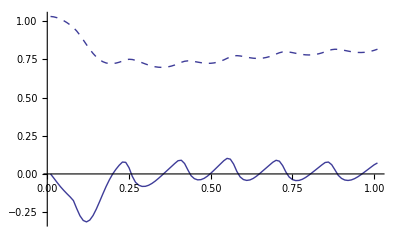

```mathematica
Needs["PlotLegends`"]
pa = PlotAgainstTime["length_n_0", {PlotStyle->{Dashed}, PlotRange-> All}];
pb = PlotAgainstTime["velocity_n_0",{PlotRange-> All}];
Show[pa,pb, PlotRange-> All,  AxesOrigin->{0,0}]
```

```mathematica
length = NtoD["length_n_0"];
vel = Evaluate[NtoD["velocity_n_0"]];
data3d = Transpose[{time, length, vel}];
Show[Graphics3D[Line[data3d]], Axes->True, BoxRatios->{1,1,1}]
```

-Graphics3D-

### Reconstructed force curves

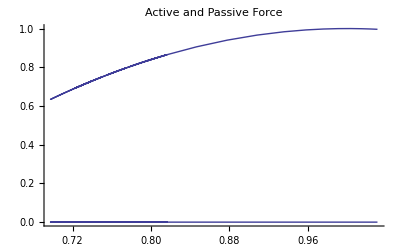

```mathematica
actForce = PlotAgainst["length_n_0", "activeForce_0",{}];
psvForce = PlotAgainst["length_n_0", "passiveForce_0",{}];
Show[actForce, psvForce,PlotRange->All, AxesOrigin->{0,0}, PlotLabel->"Active and Passive Force"]
```

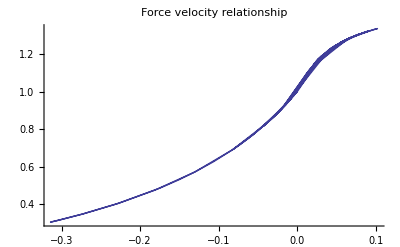

```mathematica
velForce = PlotAgainst["velocity_n_0", "velocityForce_0",{PlotRange->All, AxesOrigin->{0,0}, PlotLabel->"Force velocity relationship"}]
```